```mathematica
(* Potential, without normalization *)
V[θ_] =θ ^2; (*θ is now ϕ/μ*)

(* Putting in required known constants *)
m = 1.2209*10^28 ; (*Non-reduced Planck Mass, Subscript[m, pl], in eV/c^2 *)
Mmin = 0.5; (*M is Subscript[m, pl]/μ *)
Mmax = 2;
wmin=-1/3; (*most conservative lower bound on w*)
wmax = 1; (*most conservative upper bound on w*)
δ = 4.5*10^-5 ;(*I think this is the current value I'm using*)
T0 = 2.72548/(1.16*10^4);(*current CMB temp in eV*)

(* Slow-roll parameters *)
HH[θ_]=Sqrt[V[θ]];
ϵ[θ_,M_] = M^2/(4π)(HH'[θ]/HH[θ])^2;
η[θ_,M_] = M^2/(4 π)(HH''[θ]/HH[θ]) ;

ξ[ θ_,M_] = M^4/(16 π^2)((HH'[θ] HH'''[θ])/(HH[θ])^2);

σ[ θ_,M_] = 2 η[θ,M] - 4 ϵ[θ,M];
(* Field Value at the end of inflation *)

(*θe[M_] := Abs[Re[X/. FindRoot[ϵ[X,M]==1,{X,0.8}]]]*)(*Use this one for the 1-θ^x potentia*)

θe[M_] := Abs[Re[X/. FindRoot[ϵ[X,M]==1,{X,M/Sqrt[π]}]]](*use this one for the others*)

(*θe[M_] := Abs[Re[X/. FindRoot[ϵ[X,M]==1,{X,Sqrt[3/(16 π)]M}]]]*)(*aand this one for Starobinksy*)


Nume[θ_?NumberQ,M_]:=Re[(8π/M^2) NIntegrate[V[b]/V'[b],{b, θe[M],θ}]]

(* Field value NN e-folds before the end of inflation. Exact answer: *)
θN[NN_,M_] := Re[xx/. FindRoot[Nume[xx,M] == NN, {xx,1.5}]]
(* Observables *)
CC = 0.0814514;
r[NN_,M_] := Re[16.0ϵ[θN[NN,M],M] (1 - CC ( σ[θN[NN,M],M] + 2 ϵ[θN[NN,M],M]))]
n[NN_,M_] := Re[1 + σ[θN[NN,M],M] - (5 - 3 CC) ϵ[θN[NN,M],M]^2 - 1/4(3 - 5 CC) σ[θN[NN,M],M] ϵ[θN[NN,M],M] + 1/2 (3 - CC) ξ [θN[NN,M],M]]

(* Normalization *)
Vend[NN_,M_]:= (3 δ^2 M^2)/(128π)(V'[θN[NN,M]]/V[θN[NN,M]])^2(V[θe[M]]/V[θN[NN,M]])
V0[NN_,M_]:= (3 δ^2 M^2)/(128π)(V'[θN[NN,M]]/V[θN[NN,M]])^2(1/V[θN[NN,M]]) (*This is my normalization coefficient*)
HN[NN_,M_]:=m*√((8 π)/(3 M^2)V0[NN,M]*V[θN[NN,M]]) (*Normalized and correct Hk--the extra m in front is because I had forgotten for a while that there is an mpl factor that I had dropped everywhere, since it wound up cancelling/dropping in the end because the first method for Nk has log Trh/mpl, but I need the mpl here. Anyway, I can simplify, but somehow that results in complex answers, whereas this way I get real ones, so...not simplifying.*)

(*Known Parameters*)
Ωmh2 = 0.14212;
aeq=(4.15*10^-5)/Ωmh2; (*I'm actually not sure what to make of this, because I get something like 3.5*10^-4 this way, but if I go by zeq, I get that aeq should be about 2.9*10^-4. I'm not at all sure if this matters, though. *)
a0 = 1; (*I'm pretty sure I can say this*)
H0 = 67.26*3.241*10^-20*6.58*10^-16; (*Converting from km/s/Mpc to eV*)
Ωm = 0.316; (*This appears to be the most recent Planck number*)
Heq = (2Ωm*H0^2*aeq^-3)^(1/2); (*From an equation for H(y), found here: http://www.tapir.caltech.edu/~chirata/ph217/lec06.pdf *)
pivotk = 3.2*10^-31; (*0.05 Mpc^-1 in eV*)
g[Tre_]=Piecewise[{{100, Tre⩾10^9}, {10, 10^6<Tre<10^9}, {3, Tre≤10^6}}];
Treh = T0*(43/(11*3))^(1/3)*1/aeq*1/0.00001;
(*Insert calculation for NRD here*)

NRD[Tre_] := -Log[T0/Tre(43/(11*g[Tre]))^(1/3)*1/aeq] (*TURNS OUT THIS IS DEPENDANT ON REHEAT TEMP, so I had to run through a separate equation, and I get this. Important! *)

(*Getting Nre from the foregoing*)
Nre[NN_,M_,Tre_]:=-NN-NRD[Tre]+Log[(aeq*Heq)/pivotk]+Log[HN[NN,M]/Heq]
(* Reheat Temperature *)
Trh[NN_,M_,w_,Tre_]:=m*Exp[-3/4(1+w)Nre[NN,M,Tre]](30/(g[Tre] π^2))^(1/4)(1+1/2)^(1/4)Vend[NN,M]^(1/4)
(* Min N *)
Nm2[M_,w_,Tre_]:= Re[xyy/. FindRoot[Trh[xyy,M,w,Tre]==Tre,{xyy,45}]]
```

```mathematica
(*Test Plotting for Mass Range*)
n[Nm2[Mmin,0,Treh],Mmin]
r[Nm2[Mmin,0,Treh],Mmin]
n[Nm2[Mmax,0,Treh],Mmax]
r[Nm2[Mmax,0,Treh],Mmax]
```

FindRoot::nlnum: The function value {56.0487-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {1.5}.

ReplaceAll::reps: {FindRoot[Nume[xx,0.5]==xyy,{xx,1.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {56.0487-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {1.5}.

ReplaceAll::reps: {FindRoot[Nume[xx,0.5]==xyy,{xx,1.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {56.0487-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {1.5}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,0.5]==xyy,{xx,1.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

0.953788

FindRoot::nlnum: The function value {56.0487-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {1.5}.

ReplaceAll::reps: {FindRoot[Nume[xx,0.5]==xyy,{xx,1.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {56.0487-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {1.5}.

ReplaceAll::reps: {FindRoot[Nume[xx,0.5]==xyy,{xx,1.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {56.0487-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {1.5}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,0.5]==xyy,{xx,1.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

0.184051

FindRoot::nlnum: The function value {3.03429-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {1.5}.

ReplaceAll::reps: {FindRoot[Nume[xx,2]==xyy,{xx,1.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {3.03429-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {1.5}.

ReplaceAll::reps: {FindRoot[Nume[xx,2]==xyy,{xx,1.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {3.03429-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {1.5}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,2]==xyy,{xx,1.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

0.952253

FindRoot::nlnum: The function value {3.03429-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {1.5}.

ReplaceAll::reps: {FindRoot[Nume[xx,2]==xyy,{xx,1.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {3.03429-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {1.5}.

ReplaceAll::reps: {FindRoot[Nume[xx,2]==xyy,{xx,1.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {3.03429-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {1.5}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,2]==xyy,{xx,1.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

0.190139

```mathematica
(*Generating Observables*)
dn[Tr_,M_,w_]:=D[n[Nm2[M,w,Tr],M],Tr]
rk[Tr_,M_,w_]:=r[Nm2[M,w,Tr],M] (0.05/0.002)^(1-n[Nm2[M,w,Tr],M]-r[Nm2[M,w,Tr],M]/8)
SetDirectory["/home/nina/Code/Olwen/Olwen/Coding/Research"]
M =1.0;
w=0.0;
ns[NN_,M_]:=1-4ϵ[θN[NN,M],M]+2η[θN[NN,M],M]
Tt= Log10[Treh]
TR[TT_]:=10^TT
```

/home/nina/Code/Olwen/Olwen/Coding/Research

4.94391

```mathematica
Export["Squared0.dat",Table[{n[Nm2[M,w,TR[T]],M],r[Nm2[M,w,TR[T]],M],Nm2[M,w,TR[T]]},{T,Tt,25,1}],"Data"]
```

FindRoot::nlnum: The function value {13.6372-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {1.5}.

ReplaceAll::reps: {FindRoot[Nume[xx,1.]==xyy,{xx,1.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {13.6372-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {1.5}.

ReplaceAll::reps: {FindRoot[Nume[xx,1.]==xyy,{xx,1.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {13.6372-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {1.5}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,1.]==xyy,{xx,1.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Export["SquaredM.dat",Table[{n[Nm2[Mm,w,Tt],Mm],r[Nm2[Mm,w,Tt],Mm],Nm2[Mm,w,Tt]},{Mm,Mmin,Mmax,0.05}],"Data"]
```

FindRoot::nlnum: The function value {56.0487-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {1.5}.

ReplaceAll::reps: {FindRoot[Nume[xx,0.5]==xyy,{xx,1.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {56.0487-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {1.5}.

ReplaceAll::reps: {FindRoot[Nume[xx,0.5]==xyy,{xx,1.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {56.0487-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {1.5}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,0.5]==xyy,{xx,1.5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

SquaredM.dat

```mathematica
Nm2[1,0,Treh]
Nm2[1,1/3,10^25]
```

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {0.0940316}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {0.0940316}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {0.0940316}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

41.3034

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {0.0940316}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {0.0940316}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {0.0940316}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

56.6795

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {0.0940316}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {0.0940316}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {0.0940316}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

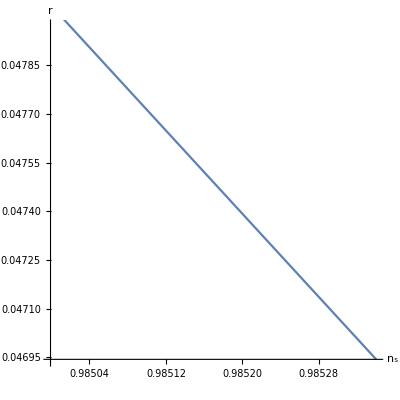

```mathematica
ParametricPlot[{n[Nm2[1,0,Tre],1],r[Nm2[1,0,Tre],1]},{Tre,Treh,10^25},AspectRatio->1,AxesLabel->{Subscript[n, s],r}]
```

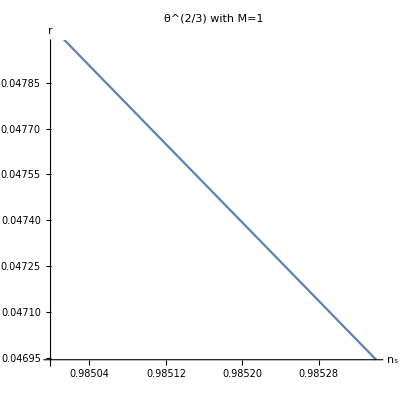

```mathematica
Show[%35,PlotLabel->HoldForm[θ^(2/3) with M=1],LabelStyle->{GrayLevel[0]}]
```

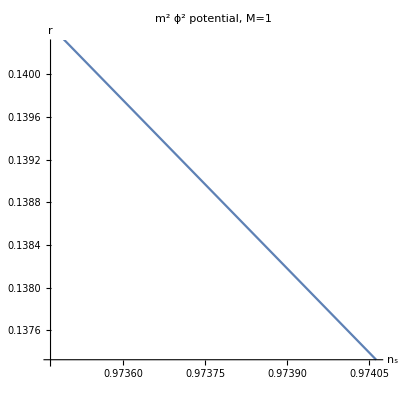

```mathematica
Show[%36,PlotLabel->RawBoxes[RowBox[{RowBox[{SuperscriptBox["m","2"],SuperscriptBox["ϕ","2"]," ","potential"}],","," ",RowBox[{"M","=","1"}]}]],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Nm2[1,1/3,2.70164*10^24]
```

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

56.7897

```mathematica
(*Consistency Check*)
Plot[Trh[Nm2[1,0,Tre],1,0,Tre]/Tre,{Tre,Treh,10^24},PlotRange->{0.999,1.001}]
```

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-Graphics-

```mathematica
(*Behavioral Check*)
```

```mathematica
ParametricPlot[{n[Nm2[1,0,Tre],1],Trh[Nm2[1,0,Tre],1,0,Tre]},{Tre,Treh,10^24},AspectRatio->1]
```

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-Graphics-

```mathematica
ParametricPlot[{{n[Nm2[1,1/3,Tre],1],Trh[Nm2[1,1/3,Tre],1,1/3,Tre]},{n[Nm2[1,0,Tre],1],Trh[Nm2[1,0,Tre],1,0,Tre]},{n[Nm2[1,-1/3,Tre],1],Trh[Nm2[1,-1/3,Tre],1,-1/3,Tre]},{n[Nm2[1,0.25,Tre],1],Trh[Nm2[1,0.25,Tre],1,0.25,Tre]}},{Tre,Treh,5*10^24}, PlotLegends->{"w=1/3","w=0","w=-1/3","w=0.25"},AspectRatio->1]
```

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-Graphics-

```mathematica
(*Behavioral Checks*)
(*Plot[Nre[Nk,1],{Nk,40,60}]*)
Plot[Trh[Nk,1,0],{Nk,40,60}](*I'm doing this so as to save time when I try to plot*)
Plot[Nm2[1,w],{w,wmin,wmax}]
```

FindRoot::nlnum: The function value {0.-1. Nk} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==Nk,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. Nk} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==Nk,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. Nk} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==Nk,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

$Aborted

$Aborted

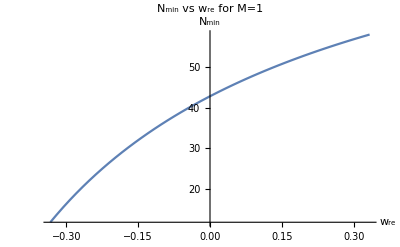

```mathematica
Show[%16,AxesLabel->{HoldForm[Subscript[w, re]],HoldForm[Subscript[N, min]]},PlotLabel->HoldForm[Subscript[N, min] vs Subscript[w, re] for M=1],LabelStyle->{GrayLevel[0]}]
```

FindRoot::srect: Value 0.56419 MM in search specification {X,MM/(√π)} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[ϵ[X,MM]==1,{X,MM/(√π)}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value 0.56419 MM in search specification {X,MM/(√π)} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[ϵ[X,MM]==1,{X,MM/(√π)}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value 0.56419 MM in search specification {X,MM/(√π)} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[ϵ[X,MM]==1,{X,MM/(√π)}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

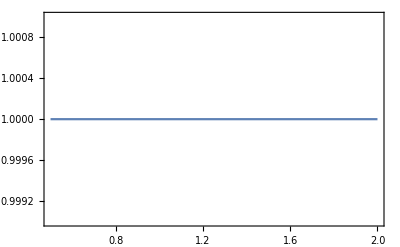

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.141056}.

ReplaceAll::reps: {FindRoot[Nume[xx,0.500031]==xyy,{xx,θe[0.500031]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.141056}.

ReplaceAll::reps: {FindRoot[Nume[xx,0.500031]==xyy,{xx,θe[0.500031]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.141056}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,0.500031]==xyy,{xx,θe[0.500031]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::srect: Value 0.56419 MM in search specification {X,MM/(√π)} is not a number or array of numbers.

FindRoot::srect: Value 0.56419 MM in search specification {X,MM 0.56419} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

-Graphics-

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {xyy} = {45.}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

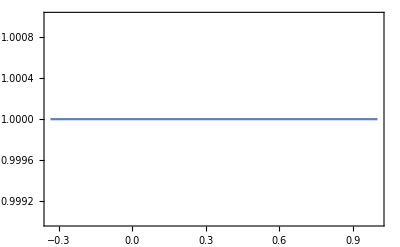

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.352618}.

ReplaceAll::reps: {FindRoot[Nume[xx,1.25]==xyy,{xx,θe[1.25]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.352618}.

ReplaceAll::reps: {FindRoot[Nume[xx,1.25]==xyy,{xx,θe[1.25]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.352618}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,1.25]==xyy,{xx,θe[1.25]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

59.9105

```mathematica
(*Consistency Checks*)
Plot[ϵ[θe[MM],MM],{MM,Mmin,Mmax},Axes->False,Frame->True,PlotRange->{0.999,1.001}] (*I have total faith in this check passing, since it is a direct carry-over from the original code, and since that's not changed, this should still work fine*)
Plot[Nume[θN[Nm2[MM,0],MM],MM]/Nm2[MM,0],{MM,Mmin,Mmax},Axes->False,Frame->True,PlotRange->{0.999,1.001}](*Here's the original consistency check with varying M, but w set at 0, for the second method*)
Plot[Nume[θN[Nm2[1,w],1],1]/Nm2[1,w],{w,wmin,wmax},Axes->False,Frame->True,PlotRange->{0.999,1.001}]
(*Consistency check with varying w and holding M constant at 1*)
```

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

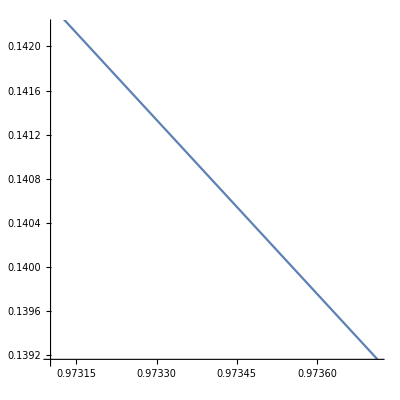

```mathematica
ParametricPlot[{n[Nm2[1,0,Tre],1],r[Nm2[1,0,Tre],1]},{Tre,Treh,10^24},AspectRatio->1]
```

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

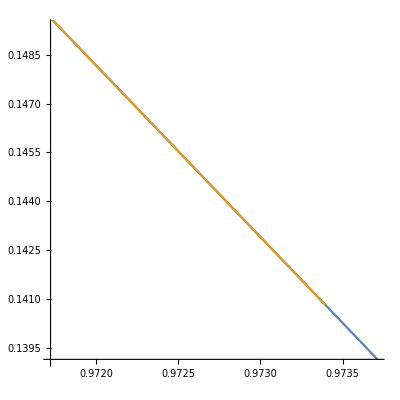

```mathematica
ParametricPlot[{{n[Nm2[1,0,Tre],1],r[Nm2[1,0,Tre],1]},{n[Nm2[1,-1/3,Tre],1],r[Nm2[1,-1/3,Tre],1]}},{Tre,Treh,10^24},AspectRatio->1]
```